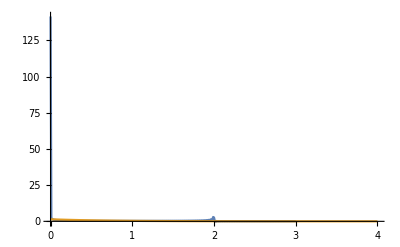

spk_pdf_smallscatt2.dat

```mathematica
(* Generates data for the speckle pdf on page 36 of Goodman. *)
(* companion to spk_analyticdis.m; the numerical integration converges here for n=2 *)

a = 1; (* amplitude of each component in the phasor sum *)
n = 2; (* number of phasors *)
s=(1-1/n)a^4; (* standard deviation *)
outa =Table[{A,2 Pi^2 NIntegrate[rho BesselJ[0,(2 Pi a rho)/(√n)]^n BesselJ[0,2 Pi √A rho],{rho,0,100},MaxRecursion->12]},{A,0,3,0.01}];
outb = Table[{A,1/(√s)Exp[-A/(√s)]},{A,0,4,0.01}]; 
ListLinePlot[{outa,outb},PlotRange->All]
Export["spk_pdf_smallscatt2.dat",outa]
```